```mathematica
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
```

TagSetDelayed::write: Tag Commutator in Commutator[a_,b_]=c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_,b_],TraditionalForm] is Protected.

Set::write: Tag Commutator in Commutator[RightPartialD[x_],LeftPartialD[y_]] is Protected.

TagSetDelayed::write: Tag Commutator in Commutator[a_,b_]=c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_,b_],TraditionalForm] is Protected.

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->NotebookDirectory[]]
```

Patched 2 FeynArts models.

```mathematica
diags=InsertFields[CreateTopologies[0,0->3],{}->{V[1,{a1}],V[1,{a2}],V[1,{a3}]},InsertionLevel->{Particles},Model->FileNameJoin[{NotebookDirectory[],"minDF2"}], GenericModel ->FileNameJoin[{NotebookDirectory[],"minDF2"}]];
```

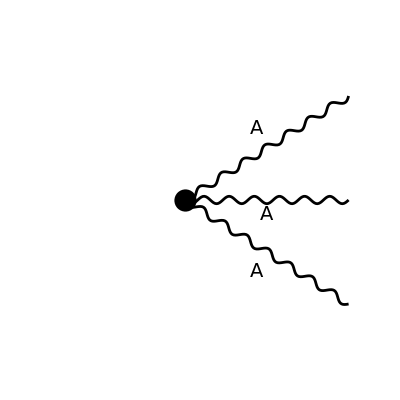

```mathematica
Paint[diags,ColumnsXRows->{3,1},Numbering->None,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags, PreFactor->1],IncomingMomenta->{},OutgoingMomenta->{p1,p2,p3},LoopMomenta->{},ChangeDimension->4,List->False];
```

```mathematica
(*FCClearScalarProducts[];
SetMandelstam[x,{ p1 , p2, p3} ,{ 0 , 0 , 0} ];*)
```

```mathematica
amp[1]=amp[0] // Contract // SUNSimplify// ExpandScalarProduct//FeynAmpDenominatorExplicit//FeynCalcExternal;
```

```mathematica
amp[2]=amp[1]/.SP[p3,p3]->0/.SP[p1,p1]->0/.SP[p2,p2]->0/.SP[x_,Polarization[x_,y_]]->0
```

-g (m^2 SP[p1,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-m^2 SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-m^2 SP[p1,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+m^2 SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+m^2 SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-m^2 SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]) SUNF[a1,a2,a3]

```mathematica
%/.m->0
```

-g (-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,p3] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,p2] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]) SUNF[a1,a2,a3]

```mathematica
diags2=InsertFields[CreateTopologies[0,2->2],{V[1,{a1}],V[1,{a2}]}->{V[1,{a3}],V[1,{a4}]},InsertionLevel->{Particles},Model->FileNameJoin[{NotebookDirectory[],"minDF2"}], GenericModel ->FileNameJoin[{NotebookDirectory[],"minDF2"}]];
```

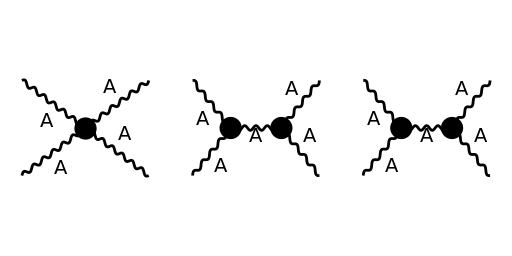

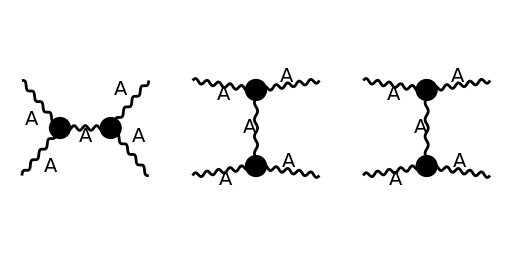

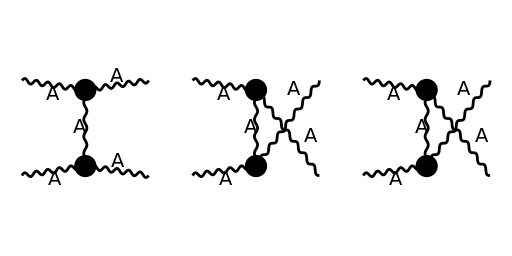

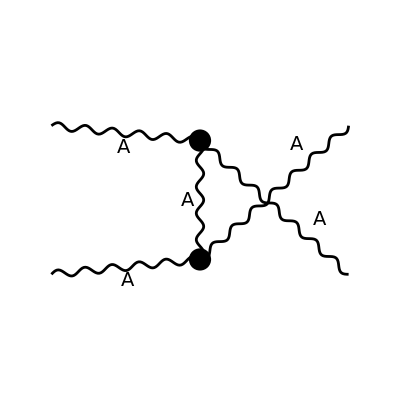

```mathematica
Paint[diags2,ColumnsXRows->{3,1},Numbering->None,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
amp2[0]=FCFAConvert[CreateFeynAmp[diags2, PreFactor->1],IncomingMomenta->{-p1,-p2},OutgoingMomenta->{p3,p4},LoopMomenta->{},ChangeDimension->4,List->False]//Contract //FeynAmpDenominatorExplicit//ExpandScalarProduct//FeynCalcExternal;
```

```mathematica
amp2[1]=amp2[0]/.SP[x_,Polarization[x_,y_]]->0/.SP[Polarization[x_,y_],Polarization[x_,y_]]->0/.SP[p3,p3]->0/.SP[p1,p1]->m^2/.SP[p2,p2]->m^2
```

1/(2 SP[p2,p3] (m^2+2 SP[p2,p3]))ⅈ (g (2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]]-2 m^2 SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,p3] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]) (g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g SP[p1,Polarization[p4,-ⅈ]] (m^2+2 SP[p2,p3]) SP[p3,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g m^2 SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g (-SP[p1,p2]-SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g SP[p1,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p3]) SP[p3,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g m^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g m^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g SP[p3,Polarization[-p1,ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g (m^2+2 SP[p2,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g m^2 SP[p1,p3] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g m^2 SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g (-SP[p1,p2]-SP[p1,p3]) SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g SP[p1,p3] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g SP[p2,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g m^2 SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g (m^2+2 SP[p2,p3]) SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g SP[p1,p3] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g SP[p2,p3] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]) SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]]+g (2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]]+2 SP[p2,p3] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]) (-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] (-m^2-SP[p2,p3]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p2,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g SP[p1,Polarization[p4,-ⅈ]] (m^2+2 SP[p2,p3]) SP[p2,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g (-SP[p1,p2]-SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g SP[p1,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p3]) SP[p2,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g SP[p1,Polarization[p4,-ⅈ]] (-m^2-SP[p2,p3]) (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g m^2 SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g m^2 SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g SP[p1,p2] SP[p1,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g SP[p1,Polarization[-p1,ⅈ]] (-m^2-SP[p2,p3]) (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g m^2 SP[p2,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[-p1,ⅈ]] SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g SP[p2,Polarization[-p1,ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g (m^2+2 SP[p2,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g (-m^2-SP[p2,p3]) (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g m^2 SP[p1,p2] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g m^2 (-m^2-SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g (-SP[p1,p2]-SP[p1,p3]) (-m^2-SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g SP[p1,p2] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g m^2 SP[p2,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g (m^2+2 SP[p2,p3]) SP[p2,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g (m^2+SP[p2,p3]) (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g SP[p1,p2] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g (m^2+SP[p2,p3]) SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]) SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]]+(g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (m^2+2 SP[p2,p3]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p2,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+4 g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3]^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 m^2 SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 m^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 SP[p1,p2] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g^2 SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3]^2 (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 m^2 SP[p2,p3] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g^2 SP[p2,p3] SP[p2,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g^2 SP[p2,p3] SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 SP[p2,p3] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g^2 SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g^2 m^2 SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-4 g^2 SP[p2,p3]^2 (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g^2 SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p3]^2 SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 m^2 SP[p2,p3] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 SP[p1,p2] SP[p2,p3] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 SP[p1,p3] SP[p2,p3] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p2,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g^2 m^2 SP[p2,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g^2 SP[p2,p3]^2 (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p3] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]) SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]]+(g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g^2 SP[p1,Polarization[p4,-ⅈ]] (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p2,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g^2 (SP[p1,p2]+SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 SP[p1,Polarization[-p1,ⅈ]] (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g^2 SP[p1,Polarization[p4,-ⅈ]] (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+4 g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3]^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 m^2 SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g^2 (SP[p1,p2]+SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 SP[p1,Polarization[-p1,ⅈ]] (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 m^2 SP[p2,p3] (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 m^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 SP[p1,p2] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g^2 SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3]^2 (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 SP[p2,p3] (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g^2 SP[p2,p3] SP[p2,Polarization[-p1,ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g^2 SP[p2,p3] SP[p3,Polarization[-p1,ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g^2 (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g^2 (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g^2 m^2 SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-4 g^2 SP[p2,p3]^2 (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 m^2 (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 SP[p1,p2] (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 SP[p1,p3] (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,p3]^2 SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p2,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g^2 m^2 SP[p2,p3] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g^2 SP[p2,p3]^2 (SP[p2,p4]+SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,p3] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g^2 SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]) SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]]+g (-2 m^2 SP[p2,Polarization[p3,-ⅈ]]-4 SP[p2,p3] SP[p2,Polarization[p3,-ⅈ]]) (-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[-p2,ⅈ]]-SP[p3,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) (-SP[p2,Polarization[-p2,ⅈ]]-SP[p3,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[-p2,ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g SP[p1,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[-p2,ⅈ]]-SP[p3,Polarization[-p2,ⅈ]]) (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g (-SP[p2,Polarization[-p2,ⅈ]]-SP[p3,Polarization[-p2,ⅈ]]) (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g m^2 SP[p1,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g SP[p1,Polarization[p4,-ⅈ]] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g m^2 (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g SP[p1,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g m^2 SP[p1,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g SP[p1,Polarization[-p2,ⅈ]] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g m^2 (-SP[p2,Polarization[-p2,ⅈ]]-SP[p3,Polarization[-p2,ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g (-SP[p1,p2]-SP[p1,p3]) (-SP[p2,Polarization[-p2,ⅈ]]-SP[p3,Polarization[-p2,ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g (-SP[p2,p4]-SP[p3,p4]) (SP[p2,Polarization[-p2,ⅈ]]+SP[p3,Polarization[-p2,ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g SP[p1,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g (SP[p2,Polarization[-p2,ⅈ]]+SP[p3,Polarization[-p2,ⅈ]]) SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g m^2 SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g (m^2+2 SP[p2,p3]) SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g (-SP[p1,p2]-SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g SP[p1,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p3]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g m^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g m^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g (m^2+2 SP[p2,p3]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]) SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]]+g (-2 m^2 SP[p3,Polarization[-p2,ⅈ]]-4 SP[p2,p3] SP[p3,Polarization[-p2,ⅈ]]) (-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g m^2 SP[p1,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+2 g SP[p1,Polarization[p4,-ⅈ]] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g m^2 (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g SP[p1,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g m^2 SP[p1,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g SP[p1,Polarization[p3,-ⅈ]] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g m^2 SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g (-SP[p1,p2]-SP[p1,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g SP[p1,Polarization[p3,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g SP[p2,Polarization[p3,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g m^2 SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g (m^2+2 SP[p2,p3]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g (-SP[p1,p2]-SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g SP[p1,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p3]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g m^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g m^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g SP[p1,Polarization[-p1,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-2 g (m^2+2 SP[p2,p3]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]) SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]])+1/(2 SP[p2,p3] (m^2+2 SP[p2,p3]))ⅈ (g (2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]]-2 m^2 SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,p3] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]) (g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g SP[p1,Polarization[p4,-ⅈ]] (m^2+2 SP[p2,p3]) SP[p3,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g m^2 SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g (-SP[p1,p2]-SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g SP[p1,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p3]) SP[p3,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g m^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g m^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g SP[p3,Polarization[-p1,ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g (m^2+2 SP[p2,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g m^2 SP[p1,p3] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g m^2 SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g (-SP[p1,p2]-SP[p1,p3]) SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g SP[p1,p3] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g SP[p2,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g m^2 SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g (m^2+2 SP[p2,p3]) SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g SP[p1,p3] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g SP[p2,p3] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]) SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[2]]+g (2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]]+2 SP[p2,p3] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]) (-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] (-m^2-SP[p2,p3]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p2,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g SP[p1,Polarization[p4,-ⅈ]] (m^2+2 SP[p2,p3]) SP[p2,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g (-SP[p1,p2]-SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g SP[p1,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p3]) SP[p2,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g SP[p1,Polarization[p4,-ⅈ]] (-m^2-SP[p2,p3]) (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g m^2 SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g m^2 SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g SP[p1,p2] SP[p1,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g SP[p1,Polarization[-p1,ⅈ]] (-m^2-SP[p2,p3]) (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g m^2 SP[p2,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[-p1,ⅈ]] SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g SP[p2,Polarization[-p1,ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g (m^2+2 SP[p2,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g (-m^2-SP[p2,p3]) (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g m^2 SP[p1,p2] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g m^2 (-m^2-SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g (-SP[p1,p2]-SP[p1,p3]) (-m^2-SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g SP[p1,p2] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g m^2 SP[p2,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g (m^2+2 SP[p2,p3]) SP[p2,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g (m^2+SP[p2,p3]) (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g SP[p1,p2] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g (m^2+SP[p2,p3]) SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]) SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[2]]+(g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (m^2+2 SP[p2,p3]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p2,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+4 g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3]^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 m^2 SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 m^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 SP[p1,p2] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g^2 SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3]^2 (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 m^2 SP[p2,p3] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g^2 SP[p2,p3] SP[p2,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g^2 SP[p2,p3] SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 SP[p2,p3] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g^2 SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g^2 m^2 SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-4 g^2 SP[p2,p3]^2 (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g^2 SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p3]^2 SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 m^2 SP[p2,p3] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 SP[p1,p2] SP[p2,p3] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 SP[p1,p3] SP[p2,p3] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p2,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g^2 m^2 SP[p2,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g^2 SP[p2,p3]^2 (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p3] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]) SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[2]]+(g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g^2 SP[p1,Polarization[p4,-ⅈ]] (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p2,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g^2 (SP[p1,p2]+SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 SP[p1,Polarization[-p1,ⅈ]] (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g^2 SP[p1,Polarization[p4,-ⅈ]] (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+4 g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3]^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 m^2 SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g^2 (SP[p1,p2]+SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 SP[p1,Polarization[-p1,ⅈ]] (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 m^2 SP[p2,p3] (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 m^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 SP[p1,p2] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g^2 SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3]^2 (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 SP[p2,p3] (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g^2 SP[p2,p3] SP[p2,Polarization[-p1,ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g^2 SP[p2,p3] SP[p3,Polarization[-p1,ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g^2 (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g^2 (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g^2 m^2 SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-4 g^2 SP[p2,p3]^2 (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 m^2 (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 SP[p1,p2] (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 SP[p1,p3] (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,p3]^2 SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p2,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g^2 m^2 SP[p2,p3] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g^2 SP[p2,p3]^2 (SP[p2,p4]+SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,p3] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g^2 SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]) SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[2]]+g (-2 m^2 SP[p2,Polarization[p3,-ⅈ]]-4 SP[p2,p3] SP[p2,Polarization[p3,-ⅈ]]) (-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[-p2,ⅈ]]-SP[p3,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) (-SP[p2,Polarization[-p2,ⅈ]]-SP[p3,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[-p2,ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g SP[p1,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[-p2,ⅈ]]-SP[p3,Polarization[-p2,ⅈ]]) (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g (-SP[p2,Polarization[-p2,ⅈ]]-SP[p3,Polarization[-p2,ⅈ]]) (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g m^2 SP[p1,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g SP[p1,Polarization[p4,-ⅈ]] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g m^2 (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g SP[p1,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g m^2 SP[p1,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g SP[p1,Polarization[-p2,ⅈ]] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g m^2 (-SP[p2,Polarization[-p2,ⅈ]]-SP[p3,Polarization[-p2,ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g (-SP[p1,p2]-SP[p1,p3]) (-SP[p2,Polarization[-p2,ⅈ]]-SP[p3,Polarization[-p2,ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g (-SP[p2,p4]-SP[p3,p4]) (SP[p2,Polarization[-p2,ⅈ]]+SP[p3,Polarization[-p2,ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g SP[p1,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g (SP[p2,Polarization[-p2,ⅈ]]+SP[p3,Polarization[-p2,ⅈ]]) SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g m^2 SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g (m^2+2 SP[p2,p3]) SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g (-SP[p1,p2]-SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g SP[p1,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p3]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g m^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g m^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g (m^2+2 SP[p2,p3]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]) SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[2]]+g (-2 m^2 SP[p3,Polarization[-p2,ⅈ]]-4 SP[p2,p3] SP[p3,Polarization[-p2,ⅈ]]) (-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g m^2 SP[p1,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+2 g SP[p1,Polarization[p4,-ⅈ]] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g m^2 (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g SP[p1,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g m^2 SP[p1,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g SP[p1,Polarization[p3,-ⅈ]] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g m^2 SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g (-SP[p1,p2]-SP[p1,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g SP[p1,Polarization[p3,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g SP[p2,Polarization[p3,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g m^2 SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g (m^2+2 SP[p2,p3]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g (-SP[p1,p2]-SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g SP[p1,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p3]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g m^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g m^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g SP[p1,Polarization[-p1,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-2 g (m^2+2 SP[p2,p3]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]) SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[2]])+1/(2 SP[p2,p3] (m^2+2 SP[p2,p3]))ⅈ (g (2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]]-2 m^2 SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,p3] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]) (g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g SP[p1,Polarization[p4,-ⅈ]] (m^2+2 SP[p2,p3]) SP[p3,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g m^2 SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g (-SP[p1,p2]-SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g SP[p1,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p3]) SP[p3,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g m^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g m^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g SP[p3,Polarization[-p1,ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g (m^2+2 SP[p2,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g m^2 SP[p1,p3] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g m^2 SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g (-SP[p1,p2]-SP[p1,p3]) SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g SP[p1,p3] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g SP[p2,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g m^2 SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g (m^2+2 SP[p2,p3]) SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g SP[p1,p3] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g SP[p2,p3] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]) SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[3]]+g (2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]]+2 SP[p2,p3] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]) (-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] (-m^2-SP[p2,p3]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p2,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g SP[p1,Polarization[p4,-ⅈ]] (m^2+2 SP[p2,p3]) SP[p2,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g (-SP[p1,p2]-SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g SP[p1,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p3]) SP[p2,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g SP[p1,Polarization[p4,-ⅈ]] (-m^2-SP[p2,p3]) (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g m^2 SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g m^2 SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g SP[p1,p2] SP[p1,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g SP[p1,Polarization[-p1,ⅈ]] (-m^2-SP[p2,p3]) (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g m^2 SP[p2,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[-p1,ⅈ]] SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g SP[p2,Polarization[-p1,ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g (m^2+2 SP[p2,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g (-m^2-SP[p2,p3]) (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g m^2 SP[p1,p2] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g m^2 (-m^2-SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g (-SP[p1,p2]-SP[p1,p3]) (-m^2-SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g SP[p1,p2] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g m^2 SP[p2,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g (m^2+2 SP[p2,p3]) SP[p2,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g (m^2+SP[p2,p3]) (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g SP[p1,p2] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g (m^2+SP[p2,p3]) SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]) SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[3]]+(g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (m^2+2 SP[p2,p3]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p2,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+4 g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3]^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 m^2 SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 m^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 SP[p1,p2] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g^2 SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3]^2 (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 m^2 SP[p2,p3] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g^2 SP[p2,p3] SP[p2,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g^2 SP[p2,p3] SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 SP[p2,p3] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g^2 SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g^2 m^2 SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-4 g^2 SP[p2,p3]^2 (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g^2 SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p3]^2 SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 m^2 SP[p2,p3] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 SP[p1,p2] SP[p2,p3] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 SP[p1,p3] SP[p2,p3] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p2,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g^2 m^2 SP[p2,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g^2 SP[p2,p3]^2 (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p3] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]) SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[3]]+(g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g^2 SP[p1,Polarization[p4,-ⅈ]] (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p2,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g^2 (SP[p1,p2]+SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 SP[p1,Polarization[-p1,ⅈ]] (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g^2 SP[p1,Polarization[p4,-ⅈ]] (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+4 g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3]^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 m^2 SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g^2 (SP[p1,p2]+SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 SP[p1,Polarization[-p1,ⅈ]] (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 m^2 SP[p2,p3] (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 m^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 SP[p1,p2] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g^2 SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3]^2 (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 SP[p2,p3] (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g^2 SP[p2,p3] SP[p2,Polarization[-p1,ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g^2 SP[p2,p3] SP[p3,Polarization[-p1,ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g^2 (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g^2 (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g^2 m^2 SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-4 g^2 SP[p2,p3]^2 (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 m^2 (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 SP[p1,p2] (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 SP[p1,p3] (-m^2-2 SP[p2,p3]) SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,p3]^2 SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p2,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g^2 m^2 SP[p2,p3] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g^2 SP[p2,p3]^2 (SP[p2,p4]+SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,p3] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g^2 SP[p2,p3] (m^2+2 SP[p2,p3]) SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]) SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[3]]+g (-2 m^2 SP[p2,Polarization[p3,-ⅈ]]-4 SP[p2,p3] SP[p2,Polarization[p3,-ⅈ]]) (-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[-p2,ⅈ]]-SP[p3,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) (-SP[p2,Polarization[-p2,ⅈ]]-SP[p3,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[-p2,ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g SP[p1,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[-p2,ⅈ]]-SP[p3,Polarization[-p2,ⅈ]]) (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g (-SP[p2,Polarization[-p2,ⅈ]]-SP[p3,Polarization[-p2,ⅈ]]) (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g m^2 SP[p1,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g SP[p1,Polarization[p4,-ⅈ]] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g m^2 (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g SP[p1,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g m^2 SP[p1,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g SP[p1,Polarization[-p2,ⅈ]] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g m^2 (-SP[p2,Polarization[-p2,ⅈ]]-SP[p3,Polarization[-p2,ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g (-SP[p1,p2]-SP[p1,p3]) (-SP[p2,Polarization[-p2,ⅈ]]-SP[p3,Polarization[-p2,ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g (-SP[p2,p4]-SP[p3,p4]) (SP[p2,Polarization[-p2,ⅈ]]+SP[p3,Polarization[-p2,ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g SP[p1,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g (SP[p2,Polarization[-p2,ⅈ]]+SP[p3,Polarization[-p2,ⅈ]]) SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g m^2 SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g (m^2+2 SP[p2,p3]) SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g (-SP[p1,p2]-SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g SP[p1,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p3]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g m^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g m^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g (m^2+2 SP[p2,p3]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]) SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[3]]+g (-2 m^2 SP[p3,Polarization[-p2,ⅈ]]-4 SP[p2,p3] SP[p3,Polarization[-p2,ⅈ]]) (-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g m^2 SP[p1,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+2 g SP[p1,Polarization[p4,-ⅈ]] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g m^2 (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g SP[p1,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g m^2 SP[p1,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g SP[p1,Polarization[p3,-ⅈ]] (m^2+2 SP[p2,p3]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g m^2 SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g (-SP[p1,p2]-SP[p1,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g SP[p1,Polarization[p3,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g SP[p2,Polarization[p3,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g m^2 SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g (m^2+2 SP[p2,p3]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g (-SP[p1,p2]-SP[p1,p3]) SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g SP[p1,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p3]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g m^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g m^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p3,Polarization[-p1,ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g SP[p1,Polarization[-p1,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g (-SP[p2,Polarization[-p1,ⅈ]]-SP[p3,Polarization[-p1,ⅈ]]) SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-2 g (m^2+2 SP[p2,p3]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]) SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[3]])-4 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28264]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28264]]+4 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28265]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28265]]+2 ⅈ g^2 SP[p1,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28266]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28266]]-2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28267]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28267]]-2 ⅈ g^2 SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28268]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28268]]+2 ⅈ g^2 SP[p3,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28269]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28269]]+2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28270]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28270]]-2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28271]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28271]]-2 ⅈ g^2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28272]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28272]]+2 ⅈ g^2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28273]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28273]]+4 ⅈ g^2 SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28274]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28274]]-4 ⅈ g^2 SP[p3,Polarization[-p2,ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28275]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28275]]-ⅈ g^2 SP[p1,p2] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28276]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28276]]+ⅈ g^2 SP[p1,p3] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28277]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28277]]+ⅈ g^2 SP[p2,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28278]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28278]]-ⅈ g^2 SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28279]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28279]]+(ⅈ (g (2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p4,-ⅈ]]+2 SP[p2,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+3 SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]) (2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p2,p3] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] (-m^2-SP[p2,p4]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g (-SP[p1,p2]-SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g SP[p1,Polarization[p3,-ⅈ]] (-m^2-SP[p2,p4]) (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g m^2 SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g m^2 SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g SP[p1,p2] SP[p1,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g SP[p1,Polarization[-p1,ⅈ]] (-m^2-SP[p2,p4]) (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g m^2 SP[p2,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g (-m^2-SP[p2,p4]) SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g m^2 SP[p1,p2] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g m^2 SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g m^2 (-m^2-SP[p2,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g (-SP[p1,p2]-SP[p1,p4]) (-m^2-SP[p2,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g (m^2+SP[p2,p4]) (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g SP[p1,p2] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g SP[p2,p3] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]) SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[1]]+g (2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p4,-ⅈ]]-2 m^2 SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]) (2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p3,p4] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,p4]-SP[p4,p4]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,p4]-SP[p4,p4]) (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g SP[p1,Polarization[p3,-ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g SP[p1,Polarization[-p1,ⅈ]] (-SP[p2,p4]-SP[p4,p4]) (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,p4]-SP[p4,p4]) (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g m^2 SP[p4,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g (-SP[p1,p2]-SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g SP[p1,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g SP[p3,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g m^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g m^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g m^2 SP[p1,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g m^2 SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g m^2 (-SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g (-SP[p1,p2]-SP[p1,p4]) (-SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g (-SP[p2,p3]-SP[p3,p4]) (SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g SP[p1,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g SP[p3,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]) SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[1]]+g (-2 m^2 SP[p2,Polarization[p4,-ⅈ]]-4 SP[p2,p4] SP[p2,Polarization[p4,-ⅈ]]-4 SP[p2,Polarization[p4,-ⅈ]] SP[p4,p4]) (2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) (-SP[p2,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[-p2,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g SP[p1,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g m^2 SP[p1,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g SP[p1,Polarization[p3,-ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g m^2 (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g m^2 SP[p1,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g m^2 SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g SP[p1,Polarization[-p2,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g SP[p3,Polarization[-p2,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g m^2 (-SP[p2,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g (-SP[p1,p2]-SP[p1,p4]) (-SP[p2,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g (-SP[p2,p3]-SP[p3,p4]) (SP[p2,Polarization[-p2,ⅈ]]+SP[p4,Polarization[-p2,ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g (-SP[p1,p2]-SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g SP[p1,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g SP[p3,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g m^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g m^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]) SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[1]]+(2 g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] SP[p2,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g^2 SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+4 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4]^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 m^2 SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] SP[p4,p4] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 m^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 SP[p1,p2] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g^2 SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4]^2 (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g^2 m^2 SP[p2,p4] SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-4 g^2 SP[p2,p4]^2 SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p4,p4] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g^2 SP[p2,p4] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g^2 SP[p2,p4] SP[p3,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 m^2 SP[p2,p4] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p2,p4]^2 SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g^2 m^2 SP[p2,p4] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g^2 SP[p2,p4]^2 (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 SP[p2,p3] SP[p2,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 SP[p2,p4] SP[p3,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p2,p4] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g^2 SP[p2,p4] (-SP[p2,p3]-SP[p3,p4]) SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 m^2 SP[p2,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 SP[p1,p2] SP[p2,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 SP[p1,p4] SP[p2,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]) SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[1]]+(2 g^2 (SP[p1,p2]+SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (SP[p2,p3]+SP[p3,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] SP[p2,Polarization[-p1,ⅈ]] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g^2 SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+4 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4]^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 m^2 SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] SP[p4,p4] (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g^2 (SP[p1,p2]+SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g^2 SP[p2,p4] SP[p3,Polarization[-p1,ⅈ]] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 m^2 SP[p2,p4] (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 m^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 SP[p1,p2] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g^2 SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4]^2 (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g^2 m^2 SP[p2,p4] SP[p3,Polarization[-p1,ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-4 g^2 SP[p2,p4]^2 SP[p3,Polarization[-p1,ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p4,p4] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g^2 SP[p2,p4] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g^2 (SP[p1,p2]+SP[p1,p4]) SP[p2,p4]^2 SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g^2 m^2 SP[p2,p4] (SP[p2,p3]+SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g^2 SP[p2,p4]^2 (SP[p2,p3]+SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 m^2 SP[p2,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 SP[p1,p2] SP[p2,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 SP[p1,p4] SP[p2,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 (SP[p1,p2]+SP[p1,p4]) SP[p2,p4] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g^2 SP[p2,p4] (SP[p2,p3]+SP[p3,p4]) SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 SP[p2,p3] SP[p2,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g^2 SP[p2,p4] SP[p3,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]) SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[1]]+g (-2 SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4]-2 m^2 SP[p4,Polarization[-p2,ⅈ]]-4 SP[p2,p4] SP[p4,Polarization[-p2,ⅈ]]-4 SP[p4,p4] SP[p4,Polarization[-p2,ⅈ]]) (-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g m^2 SP[p1,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g m^2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g (-SP[p1,p2]-SP[p1,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g m^2 SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g SP[p1,Polarization[p4,-ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g SP[p3,Polarization[p4,-ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g m^2 SP[p1,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+2 g SP[p1,Polarization[p3,-ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g m^2 (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g (-SP[p1,p2]-SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g SP[p1,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-2 g SP[p3,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g m^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g m^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]) SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[1]]))/((2 SP[p2,p4]+SP[p4,p4]) (m^2+2 SP[p2,p4]+SP[p4,p4]))+(ⅈ (g (2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p4,-ⅈ]]+2 SP[p2,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+3 SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]) (2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p2,p3] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] (-m^2-SP[p2,p4]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g (-SP[p1,p2]-SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g SP[p1,Polarization[p3,-ⅈ]] (-m^2-SP[p2,p4]) (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g m^2 SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g m^2 SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g SP[p1,p2] SP[p1,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g SP[p1,Polarization[-p1,ⅈ]] (-m^2-SP[p2,p4]) (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g m^2 SP[p2,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g (-m^2-SP[p2,p4]) SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g m^2 SP[p1,p2] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g m^2 SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g m^2 (-m^2-SP[p2,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g (-SP[p1,p2]-SP[p1,p4]) (-m^2-SP[p2,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g (m^2+SP[p2,p4]) (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g SP[p1,p2] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g SP[p2,p3] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]) SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[2]]+g (2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p4,-ⅈ]]-2 m^2 SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]) (2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p3,p4] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,p4]-SP[p4,p4]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,p4]-SP[p4,p4]) (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g SP[p1,Polarization[p3,-ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g SP[p1,Polarization[-p1,ⅈ]] (-SP[p2,p4]-SP[p4,p4]) (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,p4]-SP[p4,p4]) (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g m^2 SP[p4,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g (-SP[p1,p2]-SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g SP[p1,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g SP[p3,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g m^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g m^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g m^2 SP[p1,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g m^2 SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g m^2 (-SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g (-SP[p1,p2]-SP[p1,p4]) (-SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g (-SP[p2,p3]-SP[p3,p4]) (SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g SP[p1,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g SP[p3,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]) SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[2]]+g (-2 m^2 SP[p2,Polarization[p4,-ⅈ]]-4 SP[p2,p4] SP[p2,Polarization[p4,-ⅈ]]-4 SP[p2,Polarization[p4,-ⅈ]] SP[p4,p4]) (2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) (-SP[p2,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[-p2,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g SP[p1,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g m^2 SP[p1,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g SP[p1,Polarization[p3,-ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g m^2 (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g m^2 SP[p1,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g m^2 SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g SP[p1,Polarization[-p2,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g SP[p3,Polarization[-p2,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g m^2 (-SP[p2,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g (-SP[p1,p2]-SP[p1,p4]) (-SP[p2,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g (-SP[p2,p3]-SP[p3,p4]) (SP[p2,Polarization[-p2,ⅈ]]+SP[p4,Polarization[-p2,ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g (-SP[p1,p2]-SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g SP[p1,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g SP[p3,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g m^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g m^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]) SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[2]]+(2 g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] SP[p2,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g^2 SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+4 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4]^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 m^2 SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] SP[p4,p4] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 m^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 SP[p1,p2] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g^2 SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4]^2 (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g^2 m^2 SP[p2,p4] SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-4 g^2 SP[p2,p4]^2 SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p4,p4] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g^2 SP[p2,p4] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g^2 SP[p2,p4] SP[p3,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 m^2 SP[p2,p4] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p2,p4]^2 SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g^2 m^2 SP[p2,p4] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g^2 SP[p2,p4]^2 (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 SP[p2,p3] SP[p2,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 SP[p2,p4] SP[p3,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p2,p4] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g^2 SP[p2,p4] (-SP[p2,p3]-SP[p3,p4]) SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 m^2 SP[p2,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 SP[p1,p2] SP[p2,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 SP[p1,p4] SP[p2,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]) SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[2]]+(2 g^2 (SP[p1,p2]+SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (SP[p2,p3]+SP[p3,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] SP[p2,Polarization[-p1,ⅈ]] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g^2 SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+4 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4]^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 m^2 SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] SP[p4,p4] (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g^2 (SP[p1,p2]+SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g^2 SP[p2,p4] SP[p3,Polarization[-p1,ⅈ]] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 m^2 SP[p2,p4] (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 m^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 SP[p1,p2] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g^2 SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4]^2 (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g^2 m^2 SP[p2,p4] SP[p3,Polarization[-p1,ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-4 g^2 SP[p2,p4]^2 SP[p3,Polarization[-p1,ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p4,p4] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g^2 SP[p2,p4] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g^2 (SP[p1,p2]+SP[p1,p4]) SP[p2,p4]^2 SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g^2 m^2 SP[p2,p4] (SP[p2,p3]+SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g^2 SP[p2,p4]^2 (SP[p2,p3]+SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 m^2 SP[p2,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 SP[p1,p2] SP[p2,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 SP[p1,p4] SP[p2,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 (SP[p1,p2]+SP[p1,p4]) SP[p2,p4] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g^2 SP[p2,p4] (SP[p2,p3]+SP[p3,p4]) SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 SP[p2,p3] SP[p2,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g^2 SP[p2,p4] SP[p3,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]) SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[2]]+g (-2 SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4]-2 m^2 SP[p4,Polarization[-p2,ⅈ]]-4 SP[p2,p4] SP[p4,Polarization[-p2,ⅈ]]-4 SP[p4,p4] SP[p4,Polarization[-p2,ⅈ]]) (-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g m^2 SP[p1,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g m^2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g (-SP[p1,p2]-SP[p1,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g m^2 SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g SP[p1,Polarization[p4,-ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g SP[p3,Polarization[p4,-ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g m^2 SP[p1,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+2 g SP[p1,Polarization[p3,-ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g m^2 (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g (-SP[p1,p2]-SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g SP[p1,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-2 g SP[p3,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g m^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g m^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]) SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[2]]))/((2 SP[p2,p4]+SP[p4,p4]) (m^2+2 SP[p2,p4]+SP[p4,p4]))+(ⅈ (g (2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p4,-ⅈ]]+2 SP[p2,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+3 SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]) (2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p2,p3] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] (-m^2-SP[p2,p4]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g (-SP[p1,p2]-SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g SP[p1,Polarization[p3,-ⅈ]] (-m^2-SP[p2,p4]) (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g m^2 SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g m^2 SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g SP[p1,p2] SP[p1,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g SP[p1,Polarization[-p1,ⅈ]] (-m^2-SP[p2,p4]) (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g m^2 SP[p2,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g (-m^2-SP[p2,p4]) SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g m^2 SP[p1,p2] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g m^2 SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g m^2 (-m^2-SP[p2,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g (-SP[p1,p2]-SP[p1,p4]) (-m^2-SP[p2,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g (m^2+SP[p2,p4]) (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g SP[p1,p2] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g SP[p2,p3] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]) SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[3]]+g (2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p4,-ⅈ]]-2 m^2 SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]) (2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p3,p4] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,p4]-SP[p4,p4]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,p4]-SP[p4,p4]) (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g SP[p1,Polarization[p3,-ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g SP[p1,Polarization[-p1,ⅈ]] (-SP[p2,p4]-SP[p4,p4]) (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,p4]-SP[p4,p4]) (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g m^2 SP[p4,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g (-SP[p1,p2]-SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g SP[p1,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g SP[p3,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g m^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g m^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g m^2 SP[p1,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g m^2 SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g m^2 (-SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g (-SP[p1,p2]-SP[p1,p4]) (-SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g (-SP[p2,p3]-SP[p3,p4]) (SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g SP[p1,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g SP[p3,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]) SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[3]]+g (-2 m^2 SP[p2,Polarization[p4,-ⅈ]]-4 SP[p2,p4] SP[p2,Polarization[p4,-ⅈ]]-4 SP[p2,Polarization[p4,-ⅈ]] SP[p4,p4]) (2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) (-SP[p2,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[-p2,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g SP[p1,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g m^2 SP[p1,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g SP[p1,Polarization[p3,-ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g m^2 (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g m^2 SP[p1,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g m^2 SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g SP[p1,Polarization[-p2,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g SP[p3,Polarization[-p2,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g m^2 (-SP[p2,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g (-SP[p1,p2]-SP[p1,p4]) (-SP[p2,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g (-SP[p2,p3]-SP[p3,p4]) (SP[p2,Polarization[-p2,ⅈ]]+SP[p4,Polarization[-p2,ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g (-SP[p1,p2]-SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g SP[p1,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g SP[p3,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g m^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g m^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]) SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[3]]+(2 g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] SP[p2,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g^2 SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+4 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4]^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 m^2 SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] SP[p4,p4] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 m^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 SP[p1,p2] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g^2 SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4]^2 (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g^2 m^2 SP[p2,p4] SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-4 g^2 SP[p2,p4]^2 SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p4,p4] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g^2 SP[p2,p4] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g^2 SP[p2,p4] SP[p3,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 m^2 SP[p2,p4] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p2,p4]^2 SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g^2 m^2 SP[p2,p4] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g^2 SP[p2,p4]^2 (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 SP[p2,p3] SP[p2,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 SP[p2,p4] SP[p3,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p2,p4] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g^2 SP[p2,p4] (-SP[p2,p3]-SP[p3,p4]) SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 m^2 SP[p2,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 SP[p1,p2] SP[p2,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 SP[p1,p4] SP[p2,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]) SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[3]]+(2 g^2 (SP[p1,p2]+SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (SP[p2,p3]+SP[p3,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] SP[p2,Polarization[-p1,ⅈ]] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g^2 SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+4 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4]^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 m^2 SP[p2,p4] SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] SP[p4,p4] (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g^2 (SP[p1,p2]+SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g^2 SP[p2,p4] SP[p3,Polarization[-p1,ⅈ]] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 m^2 SP[p2,p4] (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 m^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 SP[p1,p2] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g^2 SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4]^2 (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g^2 m^2 SP[p2,p4] SP[p3,Polarization[-p1,ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-4 g^2 SP[p2,p4]^2 SP[p3,Polarization[-p1,ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p4,p4] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g^2 SP[p2,p4] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g^2 (SP[p1,p2]+SP[p1,p4]) SP[p2,p4]^2 SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g^2 m^2 SP[p2,p4] (SP[p2,p3]+SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g^2 SP[p2,p4]^2 (SP[p2,p3]+SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 m^2 SP[p2,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 SP[p1,p2] SP[p2,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 SP[p1,p4] SP[p2,p4] (-m^2-2 SP[p2,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 (SP[p1,p2]+SP[p1,p4]) SP[p2,p4] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g^2 SP[p2,p4] (SP[p2,p3]+SP[p3,p4]) SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 SP[p2,p3] SP[p2,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g^2 SP[p2,p4] SP[p3,p4] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]) SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[3]]+g (-2 SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4]-2 m^2 SP[p4,Polarization[-p2,ⅈ]]-4 SP[p2,p4] SP[p4,Polarization[-p2,ⅈ]]-4 SP[p4,p4] SP[p4,Polarization[-p2,ⅈ]]) (-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g m^2 SP[p1,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g m^2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g (-SP[p1,p2]-SP[p1,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g m^2 SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g SP[p1,Polarization[p4,-ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g SP[p3,Polarization[p4,-ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g m^2 SP[p1,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+2 g SP[p1,Polarization[p3,-ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g m^2 (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g (-SP[p1,p2]-SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g SP[p1,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-2 g SP[p3,Polarization[-p1,ⅈ]] (m^2+2 SP[p2,p4]+SP[p4,p4]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g m^2 (-SP[p2,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g m^2 (SP[p2,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]) SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[3]]))/((2 SP[p2,p4]+SP[p4,p4]) (m^2+2 SP[p2,p4]+SP[p4,p4]))-4 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28188]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28188]]+2 ⅈ g^2 SP[p1,Polarization[-p2,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28189]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28189]]-2 ⅈ g^2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28190]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28190]]-2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28191]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28191]]+2 ⅈ g^2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28192]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28192]]+4 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28193]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28193]]+4 ⅈ g^2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28194]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28194]]+2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28195]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28195]]-2 ⅈ g^2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28196]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28196]]-2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28197]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28197]]+2 ⅈ g^2 SP[p3,Polarization[-p1,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28198]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28198]]-4 ⅈ g^2 SP[p3,Polarization[-p1,ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28199]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28199]]-ⅈ g^2 SP[p1,p2] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28200]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28200]]+ⅈ g^2 SP[p1,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28201]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28201]]+ⅈ g^2 SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28202]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28202]]-ⅈ g^2 SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28203]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28203]]-ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] (-2 SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28227]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28227]]+SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28226]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28226]])-ⅈ g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] (-2 SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28231]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28231]]+SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28230]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28230]])+ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] (-SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28257]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28257]]+2 SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28256]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28256]])+ⅈ g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] (-SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28261]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28261]]+2 SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28260]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28260]])-ⅈ g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] (SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28295]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28295]]+SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28294]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28294]])-ⅈ g^2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] (SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28297]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28297]]+SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28296]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28296]])-ⅈ g^2 SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] (SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28299]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28299]]+SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28298]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28298]])-ⅈ g^2 m^2 SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] (SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28301]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28301]]+SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28300]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28300]])+ⅈ g^2 m^2 SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] (SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28303]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28303]]+SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28302]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28302]])+ⅈ g^2 m^2 SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] (SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28305]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28305]]+SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28304]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28304]])+ⅈ g^2 SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] (SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28309]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28309]]+SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$28308]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$28308]])+(ⅈ (g (-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+3 SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) (2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[-p2,ⅈ]] SP[p2,p3] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g SP[p1,Polarization[-p1,ⅈ]] SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-2 g SP[p1,p3] SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[-p2,ⅈ]] SP[p3,p4] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g SP[p1,p2] SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g (-SP[p2,p3]-SP[p2,p4]) SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g m^2 SP[p1,Polarization[-p1,ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g SP[p1,p2] SP[p1,Polarization[-p1,ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g (-SP[p1,p3]-SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-2 g SP[p1,Polarization[-p2,ⅈ]] SP[p3,Polarization[-p1,ⅈ]] (2 SP[p3,p4]+SP[p4,p4]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[-p1,ⅈ]] (2 SP[p3,p4]+SP[p4,p4]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g SP[p1,Polarization[-p1,ⅈ]] SP[p3,Polarization[-p2,ⅈ]] (2 SP[p3,p4]+SP[p4,p4]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+2 g SP[p2,Polarization[-p1,ⅈ]] SP[p3,Polarization[-p2,ⅈ]] (2 SP[p3,p4]+SP[p4,p4]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-2 g SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] (-SP[p3,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-2 g SP[p1,Polarization[-p2,ⅈ]] SP[p3,p4] (-SP[p3,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] (-SP[p3,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+3 g m^2 SP[p3,Polarization[-p2,ⅈ]] (-SP[p3,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g m^2 SP[p3,Polarization[-p2,ⅈ]] (SP[p3,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+2 g SP[p1,p3] SP[p1,Polarization[-p1,ⅈ]] (-SP[p3,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g SP[p1,Polarization[-p1,ⅈ]] SP[p3,p4] (-SP[p3,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+2 g SP[p2,Polarization[-p1,ⅈ]] SP[p3,p4] (-SP[p3,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g m^2 SP[p3,Polarization[-p1,ⅈ]] (-SP[p3,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g m^2 SP[p3,Polarization[-p1,ⅈ]] (SP[p3,Polarization[-p2,ⅈ]]+SP[p4,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g m^2 SP[p1,p3] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g m^2 SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g (-SP[p1,p3]-SP[p1,p4]) SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g (-SP[p2,p3]-SP[p2,p4]) SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g SP[p1,p3] (2 SP[p3,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g SP[p2,p3] (2 SP[p3,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]) SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[1]]+g (m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) (2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[-p2,ⅈ]] SP[p2,p4] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g SP[p1,Polarization[-p1,ⅈ]] SP[p2,p4] SP[p2,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-2 g SP[p1,p4] SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[-p2,ⅈ]] (-SP[p3,p4]-SP[p4,p4]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] (-SP[p3,p4]-SP[p4,p4]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-2 g SP[p2,p4] SP[p2,Polarization[-p2,ⅈ]] (-SP[p3,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+2 g SP[p1,Polarization[-p2,ⅈ]] (-SP[p3,p4]-SP[p4,p4]) (-SP[p3,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g SP[p2,Polarization[-p2,ⅈ]] (-SP[p3,p4]-SP[p4,p4]) (-SP[p3,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g SP[p1,p2] SP[p2,Polarization[-p2,ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g (-SP[p2,p3]-SP[p2,p4]) SP[p2,Polarization[-p2,ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-2 g SP[p1,Polarization[-p2,ⅈ]] (2 SP[p3,p4]+SP[p4,p4]) SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g SP[p2,Polarization[-p2,ⅈ]] (2 SP[p3,p4]+SP[p4,p4]) SP[p4,Polarization[-p1,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+2 g SP[p1,p4] SP[p1,Polarization[-p1,ⅈ]] (-SP[p3,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g SP[p1,Polarization[-p1,ⅈ]] (-SP[p3,p4]-SP[p4,p4]) (-SP[p3,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-2 g SP[p2,Polarization[-p1,ⅈ]] (-SP[p3,p4]-SP[p4,p4]) (-SP[p3,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g m^2 SP[p4,Polarization[-p1,ⅈ]] (-SP[p3,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g m^2 SP[p1,Polarization[-p1,ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g SP[p1,p2] SP[p1,Polarization[-p1,ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g (-SP[p1,p3]-SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g SP[p1,Polarization[-p1,ⅈ]] (2 SP[p3,p4]+SP[p4,p4]) SP[p4,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+2 g SP[p2,Polarization[-p1,ⅈ]] (2 SP[p3,p4]+SP[p4,p4]) SP[p4,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+3 g m^2 (-SP[p3,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[p4,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g m^2 (SP[p3,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[p4,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g m^2 SP[p4,Polarization[-p1,ⅈ]] (SP[p3,Polarization[-p2,ⅈ]]+SP[p4,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g m^2 SP[p1,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g m^2 SP[p2,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g m^2 (-SP[p3,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g (-SP[p1,p3]-SP[p1,p4]) (-SP[p3,p4]-SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g m^2 (SP[p3,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g (-SP[p2,p3]-SP[p2,p4]) (SP[p3,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g SP[p1,p4] (2 SP[p3,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g SP[p2,p4] (2 SP[p3,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]) SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[1]]+g (2 m^2 SP[p3,Polarization[p4,-ⅈ]]-4 SP[p3,p4] SP[p3,Polarization[p4,-ⅈ]]-4 SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4]) (-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-2 g SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-2 g SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] (-SP[p3,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] (-SP[p3,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-2 g SP[p1,Polarization[-p2,ⅈ]] (-SP[p3,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g SP[p2,Polarization[-p2,ⅈ]] (-SP[p3,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g SP[p1,Polarization[-p1,ⅈ]] (-SP[p3,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+2 g SP[p2,Polarization[-p1,ⅈ]] (-SP[p3,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g m^2 SP[p1,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g m^2 SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g SP[p1,Polarization[p3,-ⅈ]] (2 SP[p3,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g SP[p2,Polarization[p3,-ⅈ]] (2 SP[p3,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g (-SP[p1,p3]-SP[p1,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g (-SP[p2,p3]-SP[p2,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g m^2 SP[p2,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g SP[p1,p2] SP[p2,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g (-SP[p2,p3]-SP[p2,p4]) SP[p2,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-2 g SP[p1,Polarization[-p2,ⅈ]] (2 SP[p3,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g SP[p2,Polarization[-p2,ⅈ]] (2 SP[p3,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g m^2 (-SP[p3,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g m^2 (SP[p3,Polarization[-p2,ⅈ]]+SP[p4,Polarization[-p2,ⅈ]]) SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g m^2 SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g SP[p1,p2] SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g (-SP[p1,p3]-SP[p1,p4]) SP[p1,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g SP[p1,Polarization[-p1,ⅈ]] (2 SP[p3,p4]+SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+2 g SP[p2,Polarization[-p1,ⅈ]] (2 SP[p3,p4]+SP[p4,p4]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+3 g m^2 (-SP[p3,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g m^2 (SP[p3,Polarization[-p1,ⅈ]]+SP[p4,Polarization[-p1,ⅈ]]) SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]) SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[1]]+g (2 m^2 SP[p4,Polarization[p3,-ⅈ]]-4 SP[p3,p4] SP[p4,Polarization[p3,-ⅈ]]-4 SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]]) (g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+2 g SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[-p2,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+2 g SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+2 g SP[p1,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[-p1,ⅈ]]-SP[p4,Polarization[-p1,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-2 g SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g SP[p1,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-2 g SP[p2,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[-p2,ⅈ]]-SP[p4,Polarization[-p2,ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g m^2 SP[p1,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g m^2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g (-SP[p1,p3]-SP[p1,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g (-SP[p2,p3]-SP[p2,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g SP[p1,Polarization[p4,-ⅈ]] (2 SP[p3,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g SP[p2,Polarization[p4,-ⅈ]] (2 SP[p3,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIn

```mathematica
/.SUNF[SUNIndex[a1],SUNIndex[a3],x_]->0
```

```mathematica
%/.SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[FCGV[x_]]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[FCGV[x_]]]->1
```

```mathematica
%/.SUNF[y_,z_,ExplicitSUNIndex[2]] ->0
```

```mathematica
%/.SUNF[y_,z_,ExplicitSUNIndex[3]] ->0
```

```mathematica
%/.SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[FCGV[x_]]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[FCGV[x_]]]->-1
```

```mathematica
%/.SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]]->-1
```

```mathematica
%/.SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[1]]->1
```

```mathematica
%//Simplify
```

ⅈ g^2 (-1/(SP[p2,p3] (m^2+2 SP[p2,p3]))(-m^2 SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]]-m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]]-m^2 SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]]-m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]]+SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p4,p4]+SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4]+SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4]+SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4]-2 m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]]-4 SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]]-2 m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]]-4 SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]]+m^4 SP[p2,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]+2 m^2 SP[p2,p3] SP[p2,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]+m^4 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]+2 m^2 SP[p2,p3] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]+m^2 SP[p2,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]+2 SP[p2,p3] SP[p2,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]+m^2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]+2 SP[p2,p3] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]-m^4 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]-2 m^2 SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]-m^4 SP[p3,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]-2 m^2 SP[p2,p3] SP[p3,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]-m^2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]-m^2 SP[p3,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,p3] SP[p3,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]+2 m^2 SP[p1,Polarization[-p2,ⅈ]] SP[p2,p3] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+4 SP[p1,Polarization[-p2,ⅈ]] SP[p2,p3]^2 SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,p2] SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,p3] SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+2 m^2 SP[p2,p4] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,p3] SP[p2,p4] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+2 m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-2 m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p3] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-4 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p3]^2 SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+2 m^2 SP[p1,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+4 SP[p1,Polarization[-p2,ⅈ]] SP[p2,p3] SP[p2,Polarization[p3,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,p2] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-2 m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-4 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p3] SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-2 m^4 SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-6 m^2 SP[p2,p3] SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-4 SP[p2,p3]^2 SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+2 m^4 SP[p3,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+6 m^2 SP[p2,p3] SP[p3,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+4 SP[p2,p3]^2 SP[p3,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-m^2 SP[p2,p3] SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+m^4 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+m^2 SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-m^2 SP[p2,p3] SP[p2,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+m^4 SP[p3,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+m^2 SP[p2,p3] SP[p3,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+SP[p2,p3] SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+m^2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+3 SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-2 m^2 SP[p2,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-3 SP[p2,p3] SP[p2,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-m^2 SP[p3,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-SP[p2,p3] SP[p3,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-2 m^2 SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-4 SP[p2,p3]^2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+2 m^4 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+6 m^2 SP[p2,p3] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+4 SP[p2,p3]^2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+2 m^2 SP[p1,p3] SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,p2] SP[p2,p3]^2 SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,p3] SP[p2,p3]^2 SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+2 m^2 SP[p2,p3] SP[p2,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,p3]^2 SP[p2,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-2 m^4 SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-4 m^2 SP[p2,p3] SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,p3]^2 SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+2 m^2 SP[p1,p3] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,p2] SP[p2,p3] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,p3] SP[p2,p3] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-SP[p1,Polarization[p4,-ⅈ]] (m^2+4 SP[p2,p3]+SP[p4,p4]) (-SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]]+m^2 SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]+2 SP[p2,p3] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]-m^2 SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,p3] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]+m^2 SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+SP[p2,p3] SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-SP[p2,Polarization[-p1,ⅈ]] (SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]]+SP[p2,p3] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]))-2 m^2 SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-4 SP[p2,p3] SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-2 m^2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-4 SP[p2,p3] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+2 m^4 SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+8 m^2 SP[p2,p3] SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+8 SP[p2,p3]^2 SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+2 m^2 SP[p2,Polarization[-p1,ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 SP[p2,p3] SP[p2,Polarization[-p1,ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 m^2 SP[p3,Polarization[-p1,ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 SP[p2,p3] SP[p3,Polarization[-p1,ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 m^4 SP[p3,Polarization[-p2,ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-8 m^2 SP[p2,p3] SP[p3,Polarization[-p2,ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-8 SP[p2,p3]^2 SP[p3,Polarization[-p2,ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,Polarization[-p1,ⅈ]] (-m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]]+SP[p1,p2] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]]+SP[p1,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]]+SP[p1,p4] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]]-2 SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]]+2 m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p2,ⅈ]]+4 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p2,ⅈ]]-m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]]+SP[p1,p2] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]]+SP[p1,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]]+SP[p1,p4] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]]-2 SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]]+2 m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]]+4 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p3] SP[p3,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[-p2,ⅈ]] (m^2+2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]])+SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p4,p4]+SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4]-2 m^2 SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-m^2 SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+SP[p1,p2] SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-3 SP[p1,p3] SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+SP[p1,p4] SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,p3]^2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+m^4 SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+m^2 SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-m^2 SP[p1,p3] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-m^2 SP[p1,p4] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+3 m^2 SP[p2,p3] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+3 SP[p1,p2] SP[p2,p3] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-SP[p1,p3] SP[p2,p3] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-SP[p1,p4] SP[p2,p3] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,p3]^2 SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+SP[p2,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-m^2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-SP[p2,p3] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p4,-ⅈ]] (SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,p4]-m^2 SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[-p2,ⅈ]]-2 SP[p2,p3] SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[-p2,ⅈ]]+m^2 SP[p3,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+2 SP[p2,p3] SP[p3,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[p3,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-SP[p2,p3] SP[p3,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+SP[p2,p4] (SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]]+SP[p2,p3] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]))+m^4 SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+m^2 SP[p1,p2] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+m^2 SP[p1,p3] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-m^2 SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+4 m^2 SP[p2,p3] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,p2] SP[p2,p3] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,p3] SP[p2,p3] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,p4] SP[p2,p3] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+4 SP[p2,p3]^2 SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-m^2 SP[p2,Polarization[p3,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,p3] SP[p2,Polarization[p3,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-m^4 SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-m^2 SP[p1,p2] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-m^2 SP[p1,p3] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+m^2 SP[p1,p4] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-4 m^2 SP[p2,p3] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,p2] SP[p2,p3] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,p3] SP[p2,p3] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,p4] SP[p2,p3] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-4 SP[p2,p3]^2 SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+m^2 SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,p3] SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28227]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28227]]+2 SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28231]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28231]]-SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28257]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28257]]-SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28261]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28261]]-4 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28264]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28264]]+4 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28265]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28265]]+2 SP[p1,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28266]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28266]]-2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28267]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28267]]-2 SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28268]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28268]]+2 SP[p3,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28269]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28269]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28270]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28270]]-2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28271]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28271]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28272]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28272]]+2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28273]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28273]]+4 SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28274]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28274]]-4 SP[p3,Polarization[-p2,ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28275]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28275]]-SP[p1,p2] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28276]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28276]]+SP[p1,p3] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28277]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28277]]+SP[p2,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28278]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28278]]-SP[p3,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28279]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28279]]-SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28295]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28295]]-SP[p1,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28297]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28297]]-SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28299]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28299]]-m^2 SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28301]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28301]]+m^2 SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28303]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28303]]+m^2 SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28305]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28305]]+SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28309]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28309]]+((4 m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]]-8 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,p4] SP[p3,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]]-8 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4]+4 m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]]-8 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,p4] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]]-8 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[p4,Polarization[-p1,ⅈ]]+4 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-8 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p4,Polarization[p3,-ⅈ]]-4 m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+8 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,p4] SP[p3,Polarization[-p1,ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-8 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]]+8 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]]-4 m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+8 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,p4] SP[p4,Polarization[-p1,ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+8 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p4,p4] SP[p4,Polarization[-p1,ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-2 m^4 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]+8 SP[p2,Polarization[p3,-ⅈ]] SP[p3,p4]^2 SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]+2 m^2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]+12 SP[p2,Polarization[p3,-ⅈ]] SP[p3,p4] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]+4 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4]^2 SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]-2 m^4 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]+2 m^4 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]+8 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4]^2 SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]-8 SP[p2,Polarization[p4,-ⅈ]] SP[p3,p4]^2 SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]+2 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]-2 m^2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]+12 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]-12 SP[p2,Polarization[p4,-ⅈ]] SP[p3,p4] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]+4 SP[p1,Polarization[p4,-ⅈ]] SP[p4,p4]^2 SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]-4 SP[p2,Polarization[p4,-ⅈ]] SP[p4,p4]^2 SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]-2 SP[p4,p4]) (-2 SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]]+(m^2+2 SP[p3,p4]+SP[p4,p4]) SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]])+2 m^4 SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]+2 m^2 SP[p1,p2] SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]-2 m^2 SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]-2 m^2 SP[p2,p4] SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]-8 m^2 SP[p1,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]-8 m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]-4 SP[p1,p2] SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]+4 SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]+4 SP[p2,p4] SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]+16 SP[p1,Polarization[-p2,ⅈ]] SP[p3,p4]^2 SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]+8 SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4]^2 SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]+4 m^4 SP[p3,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]-8 m^2 SP[p3,p4] SP[p3,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]-4 m^2 SP[p1,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]-6 m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]-4 SP[p1,p2] SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]+4 SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]+4 SP[p2,p4] SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]+24 SP[p1,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]+12 SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]-8 m^2 SP[p3,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]+8 SP[p1,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4]^2 SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]+4 SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4]^2 SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]+4 m^4 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]-8 m^2 SP[p3,p4] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]-8 m^2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]]-2 m^4 SP[p2,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-2 m^2 SP[p1,p2] SP[p2,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+2 m^2 SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+2 m^2 SP[p2,p4] SP[p2,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+8 m^2 SP[p1,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+8 m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+4 SP[p1,p2] SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-4 SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-4 SP[p2,p4] SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-16 SP[p1,Polarization[-p2,ⅈ]] SP[p3,p4]^2 SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-8 SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4]^2 SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-4 m^4 SP[p3,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+8 m^2 SP[p3,p4] SP[p3,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+4 m^2 SP[p1,Polarization[-p2,ⅈ]] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+6 m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+4 SP[p1,p2] SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-4 SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-4 SP[p2,p4] SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-24 SP[p1,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-12 SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+8 m^2 SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-8 SP[p1,Polarization[-p2,ⅈ]] SP[p4,p4]^2 SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-4 SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4]^2 SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]-4 m^4 SP[p4,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+8 m^2 SP[p3,p4] SP[p4,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+8 m^2 SP[p4,p4] SP[p4,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]]+8 m^2 SP[p2,Polarization[-p1,ⅈ]] SP[p3,p4] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-16 SP[p2,Polarization[-p1,ⅈ]] SP[p3,p4]^2 SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-4 m^4 SP[p3,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+8 m^2 SP[p3,p4] SP[p3,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+4 m^2 SP[p2,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-24 SP[p2,Polarization[-p1,ⅈ]] SP[p3,p4] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+8 m^2 SP[p3,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-8 SP[p2,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4]^2 SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-4 m^4 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+8 m^2 SP[p3,p4] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+8 m^2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-8 m^2 SP[p2,Polarization[-p1,ⅈ]] SP[p3,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+16 SP[p2,Polarization[-p1,ⅈ]] SP[p3,p4]^2 SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+4 m^4 SP[p3,Polarization[-p1,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-8 m^2 SP[p3,p4] SP[p3,Polarization[-p1,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-4 m^2 SP[p2,Polarization[-p1,ⅈ]] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+24 SP[p2,Polarization[-p1,ⅈ]] SP[p3,p4] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-8 m^2 SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+8 SP[p2,Polarization[-p1,ⅈ]] SP[p4,p4]^2 SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+4 m^4 SP[p4,Polarization[-p1,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-8 m^2 SP[p3,p4] SP[p4,Polarization[-p1,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-8 m^2 SP[p4,p4] SP[p4,Polarization[-p1,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+2 m^2 SP[p1,p3] SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 m^2 SP[p1,p4] SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-4 SP[p1,p3] SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 SP[p1,p4] SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-m^4 SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-m^2 SP[p1,p2] SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-m^2 SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+3 m^2 SP[p2,p4] SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 m^2 SP[p1,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,p2] SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-6 SP[p2,p4] SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-8 SP[p1,Polarization[-p2,ⅈ]] SP[p3,p4]^2 SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-4 SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4]^2 SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-4 m^2 SP[p2,Polarization[-p1,ⅈ]] SP[p3,p4] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+8 SP[p2,Polarization[-p1,ⅈ]] SP[p3,p4]^2 SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-m^2 SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-6 SP[p1,p3] SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,p4] SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 m^2 SP[p1,Polarization[-p2,ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+5 m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+3 SP[p1,p2] SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+3 SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-5 SP[p2,p4] SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-16 SP[p1,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-8 SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-4 m^2 SP[p2,Polarization[-p1,ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+16 SP[p2,Polarization[-p1,ⅈ]] SP[p3,p4] SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[-p1,ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4]^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-8 SP[p1,Polarization[-p2,ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4]^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-4 SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4]^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+8 SP[p2,Polarization[-p1,ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4]^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+m^4 SP[p2,Polarization[-p2,ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+m^2 SP[p1,p2] SP[p2,Polarization[-p2,ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-3 m^2 SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+m^2 SP[p2,p4] SP[p2,Polarization[-p2,ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-4 m^2 SP[p1,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-4 m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,p2] SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+6 SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,p4] SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+8 SP[p1,Polarization[-p2,ⅈ]] SP[p3,p4]^2 SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4]^2 SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 m^4 SP[p3,Polarization[-p2,ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-8 m^2 SP[p3,p4] SP[p3,Polarization[-p2,ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p2] SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+7 SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p4] SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+8 SP[p1,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p4,p4] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p4,p4] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-8 m^2 SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 m^2 SP[p2,Polarization[-p1,ⅈ]] SP[p3,p4] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-8 SP[p2,Polarization[-p1,ⅈ]] SP[p3,p4]^2 SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-4 m^4 SP[p3,Polarization[-p1,ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+8 m^2 SP[p3,p4] SP[p3,Polarization[-p1,ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-8 SP[p2,Polarization[-p1,ⅈ]] SP[p3,p4] SP[p4,p4] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+8 m^2 SP[p3,Polarization[-p1,ⅈ]] SP[p4,p4] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-m^4 SP[p1,p3] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+m^4 SP[p1,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+m^4 SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-m^4 SP[p2,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 SP[p1,p3] SP[p3,p4]^2 SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-4 SP[p1,p4] SP[p3,p4]^2 SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-4 SP[p2,p3] SP[p3,p4]^2 SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 SP[p2,p4] SP[p3,p4]^2 SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+m^2 SP[p1,p3] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-m^2 SP[p1,p4] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-m^2 SP[p2,p3] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+m^2 SP[p2,p4] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+8 SP[p1,p3] SP[p3,p4] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-4 SP[p1,p4] SP[p3,p4] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-8 SP[p2,p3] SP[p3,p4] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 SP[p2,p4] SP[p3,p4] SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 SP[p1,p3] SP[p4,p4]^2 SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-4 SP[p2,p3] SP[p4,p4]^2 SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,Polarization[-p1,ⅈ]] (2 m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]]-4 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,p4] SP[p3,Polarization[p4,-ⅈ]]-4 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4]-2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]-2 SP[p4,p4]) (SP[p2,Polarization[-p2,ⅈ]]+2 (SP[p3,Polarization[-p2,ⅈ]]+SP[p4,Polarization[-p2,ⅈ]]))+2 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-2 m^2 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-4 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[p4,Polarization[p3,-ⅈ]]+4 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,p4] SP[p4,Polarization[p3,-ⅈ]]+4 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-8 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] SP[p3,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-4 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]]+4 SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]]-8 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]]+4 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-8 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] SP[p4,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-8 SP[p1,Polarization[p4,-ⅈ]] SP[p4,p4] SP[p4,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-2 m^4 SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-2 m^2 SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+2 m^2 SP[p1,p3] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+2 m^2 SP[p1,p4] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+8 m^2 SP[p3,p4] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+4 SP[p1,p2] SP[p3,p4] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-4 SP[p1,p3] SP[p3,p4] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-4 SP[p1,p4] SP[p3,p4] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-8 SP[p3,p4]^2 SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+6 m^2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+4 SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-4 SP[p1,p3] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-4 SP[p1,p4] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-12 SP[p3,p4] SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]-4 SP[p3,Polarization[p4,-ⅈ]] SP[p4,p4]^2 SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]]+2 m^4 SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+2 m^2 SP[p1,p2] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-2 m^2 SP[p1,p3] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-2 m^2 SP[p1,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-8 m^2 SP[p3,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-4 SP[p1,p2] SP[p3,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+4 SP[p1,p3] SP[p3,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+4 SP[p1,p4] SP[p3,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+8 SP[p3,p4]^2 SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-6 m^2 SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]-4 SP[p1,p2] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+4 SP[p1,p3] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+4 SP[p1,p4] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+12 SP[p3,p4] SP[p4,p4] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+4 SP[p4,p4]^2 SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]]+m^2 SP[p1,p3] SP[p2,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-m^2 SP[p1,p4] SP[p2,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-m^2 SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+m^2 SP[p2,p4] SP[p2,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,p4] SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,p4] SP[p2,Polarization[-p2,ⅈ]] SP[p3,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+m^4 SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+m^2 SP[p1,p2] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+m^2 SP[p1,p3] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-3 m^2 SP[p1,p4] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-4 m^2 SP[p3,p4] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,p2] SP[p3,p4] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,p3] SP[p3,p4] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+6 SP[p1,p4] SP[p3,p4] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 SP[p3,p4]^2 SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-3 SP[p1,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p4] SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+3 SP[p2,p3] SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p4] SP[p2,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-5 m^2 SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-3 SP[p1,p2] SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-3 SP[p1,p3] SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+5 SP[p1,p4] SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+8 SP[p3,p4] SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 SP[p3,Polarization[-p2,ⅈ]] SP[p4,p4]^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-m^4 SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-m^2 SP[p1,p2] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+3 m^2 SP[p1,p3] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-m^2 SP[p1,p4] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 m^2 SP[p3,p4] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,p2] SP[p3,p4] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-6 SP[p1,p3] SP[p3,p4] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,p4] SP[p3,p4] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-4 SP[p3,p4]^2 SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+m^2 SP[p4,p4] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p2] SP[p4,p4] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-7 SP[p1,p3] SP[p4,p4] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p4] SP[p4,p4] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-4 SP[p3,p4] SP[p4,p4] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,Polarization[-p2,ⅈ]] (4 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]-2 SP[p4,p4])-4 SP[p2,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]-2 SP[p4,p4]) SP[p4,Polarization[p3,-ⅈ]]+(2 SP[p2,p4] (m^2-2 SP[p3,p4]-SP[p4,p4])+(m^2-SP[p4,p4]) SP[p4,p4]+SP[p2,p3] (-2 m^2+4 SP[p3,p4]+6 SP[p4,p4])) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]))) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[1]])/((2 SP[p3,p4]+SP[p4,p4]) (-m^2+2 SP[p3,p4]+SP[p4,p4]))+2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28156]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28156]]-2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28157]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28157]]-2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28158]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28158]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28159]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28159]]-4 SP[p1,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28160]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28160]]+4 SP[p1,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28161]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28161]]+4 SP[p2,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28162]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28162]]-4 SP[p2,Polarization[-p1,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28163]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28163]]+2 SP[p1,Polarization[-p2,ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28164]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28164]]-2 SP[p2,Polarization[-p1,ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28165]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28165]]-2 SP[p1,Polarization[-p2,ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28166]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28166]]+2 SP[p2,Polarization[-p1,ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28167]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28167]]-SP[p1,p3] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28168]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28168]]+SP[p1,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28169]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28169]]+SP[p2,p3] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28170]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28170]]-SP[p2,p4] SP[Polarization[-p1,ⅈ],Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28171]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28171]]+SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28176]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28176]]+SP[p1,Polarization[-p1,ⅈ]] SP[p4,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28178]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28178]]-2 SP[p2,Polarization[-p2,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28180]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28180]]-2 SP[p1,Polarization[-p1,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28186]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28186]]+SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28204]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28204]]+SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28210]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28210]]+m^2 SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28216]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28216]]-m^2 SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28218]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28218]]-m^2 SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28220]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28220]]-SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28224]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28224]]+SP[p2,Polarization[-p2,ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] (SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28235]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28235]]-SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28234]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28234]])+SP[p1,Polarization[-p1,ⅈ]] SP[p1,Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] (SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28241]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28241]]-SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28240]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28240]])+m^2 SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] (SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28247]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28247]]-SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28246]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28246]])+m^2 SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] (-SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28249]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28249]]+SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28248]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28248]])+m^2 SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] (-SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28251]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28251]]+SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28250]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28250]])+SP[p4,p4] SP[Polarization[-p1,ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p4,-ⅈ]] (-SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28255]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28255]]+SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28254]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28254]])+SP[p2,Polarization[-p2,ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[-p1,ⅈ],Polarization[p4,-ⅈ]] (SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28283]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28283]]+2 SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28282]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28282]])+SP[p1,Polarization[-p1,ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[-p2,ⅈ],Polarization[p3,-ⅈ]] (SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28285]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28285]]+2 SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28284]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28284]])-SP[p1,Polarization[-p1,ⅈ]] SP[p3,Polarization[-p2,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] (2 SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28315]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28315]]+SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28314]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28314]])-SP[p2,Polarization[-p2,ⅈ]] SP[p4,Polarization[-p1,ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]] (2 SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$28317]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$28317]]+SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$28316]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$28316]]))

```mathematica
%/.c[2,x_,y_]c[2,z_,w_]->0
```

```mathematica
%/.c[3,x_,y_]c[3,z_,w_]->0
```